```mathematica
earth12yr = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionEarth.csv"];
jupiter12yr = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionJupiter.csv"];
```

```mathematica
e12 = ListPlot[earth12yr, PlotRange->{{-1.5,1.5},{-1.5,1.5}}];
```

```mathematica
j12 = ListPlot[jupiter12yr, PlotRange->{{-6,6},{-6,6}}];
```

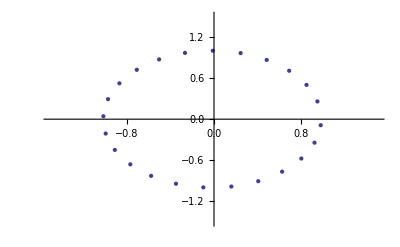

```mathematica
Show[e12,j12]
```

```mathematica
earth12yrBigJ = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionEarthBig.csv"];
jupiter12yrBigJ = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionJupiterBig.csv"];
```

```mathematica
e12BigJ = ListPlot[earth12yrBigJ, PlotRange->{{-1.5,1.5},{-1.5,1.5}}, PlotStyle->Red];
j12BigJ = ListPlot[jupiter12yrBigJ, PlotRange->{{-6,6},{-6,6}}, PlotStyle->Red];
```

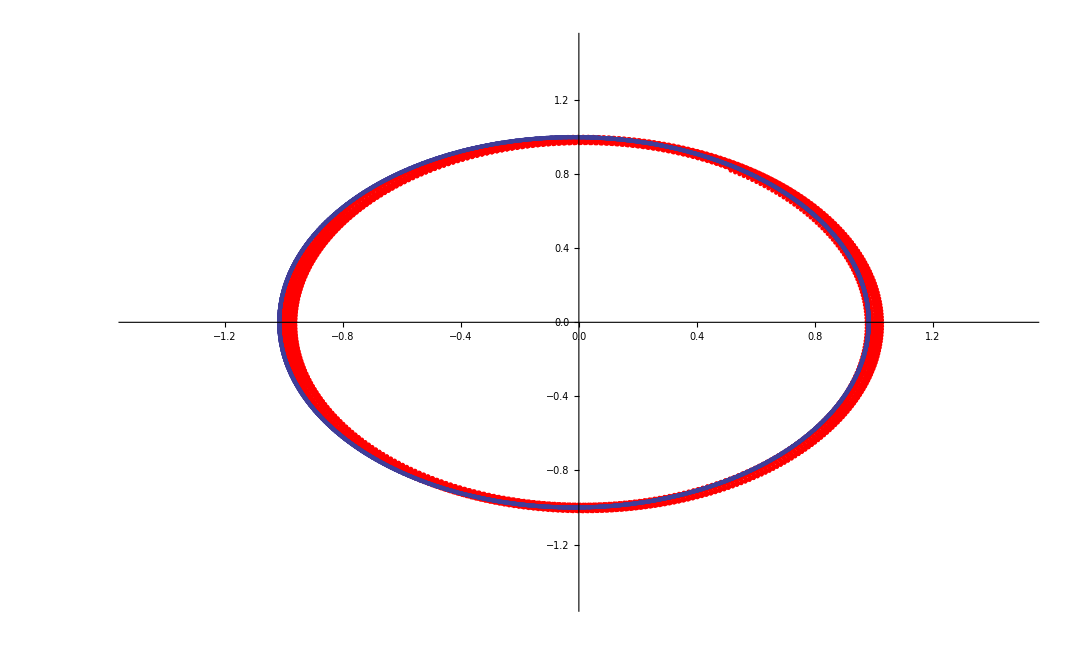

```mathematica
Show[e12BigJ,e12, j12BigJ, j12]
```

```mathematica
test = Import["/home/dk0r/git/comp-phys/HW_3/x-y-positionMercury.csv"];
```

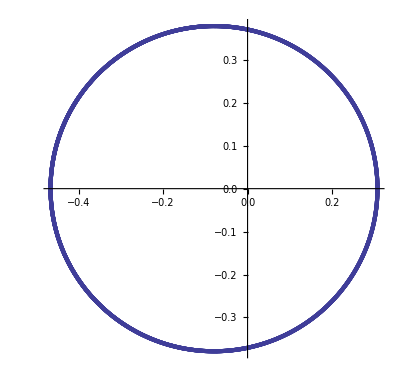

```mathematica
ListPlot[test, AspectRatio->Automatic]
```